```mathematica
ClearAll["Global`*"];
```

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)(17 + (Cos[theta])^2)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-100, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{-10.0, 45.0}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```

```mathematica
x1 = 0; x2=10;hmem=1;tb=5;μ=0; ϕ=0;
hpStep[t_, tb_]:=hmem HeavisideTheta[t-tb]
hpTanh[t_, tb_, scale_]:=hmem Tanh[scale(t-tb)]/2 + 1/2
```

```mathematica
Sstep[t_]:= 1/2 hmem(1+μ)(t-tb)HeavisideTheta[t-tb]Cos[2 ϕ]
STanh[t_, scale_]:= 1/2 hmem(1+μ)(Log[Cosh[scale(t-tb)]]/(2 scale) + (t-tb)/2)Cos[2 ϕ]
```

```mathematica
hpSacle[scale_] :=Plot[{hpStep[x, tb], hpTanh[x, tb,scale]}, {x, 0, 10}]
```

```mathematica
Manipulate[hpSacle[n], {n, 1,20}]
```

```mathematica
Resd[scale_] := Plot[{Sstep[x], STanh[x, scale]}, {x, 0, 10}]
```

```mathematica
Manipulate[Resd[n], {n, 1,20}]
```

```mathematica
generateTanhdata[scale_]:=STanh[#, scale]& /@ Range[0, 10, 0.05]
```

```mathematica
scale=1;
dataStep=Transpose@{Range[0, 10, 0.05],Map[Sstep, Range[0, 10, 0.05]]};
dataTanh=Transpose@{Range[0, 10, 0.05],generateTanhdata[scale]};
```

```mathematica
parabolaStep=Fit[dataStep,{1,x,x^2},x];
parabolaTanh=Fit[dataTanh,{1,x,x^2},x];
```

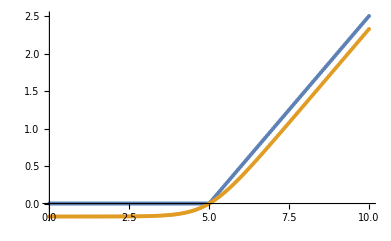

```mathematica
ListPlot[{dataStep,dataTanh }]
```

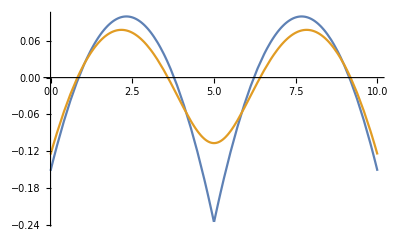

```mathematica
Plot[{Sstep[ x]-parabolaStep,STanh[x, scale]- parabolaTanh}, {x, 0, 10}]
```

```mathematica
FTStep[ω]=Simplify[FourierTransform[Sstep[ x]-parabolaStep, x,ω ]Conjugate[FourierTransform[Sstep[ x]-parabolaStep, x,ω ]]//ComplexExpand];
```

```mathematica
(*FTTanh[ω ]=Simplify[FourierTransform[STanh[x]- parabolaTanh, x,ω ]Conjugate[FourierTransform[STanh[x]- parabolaTanh, x,ω ]]//ComplexExpand];*)
```

```mathematica
Stepdata = Table[{x,Sstep[ x]-parabolaStep}, {x, Range[0, 10, 0.05]}];
Tanhdata = Table[{x,STanh[x, scale]- parabolaTanh}, {x, Range[0, 10, 0.05]}];
```

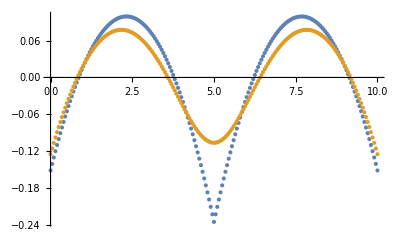

```mathematica
ListPlot[{Stepdata, Tanhdata}]
```

```mathematica
Extract[Stepdata, {All,2}];
```

```mathematica
dctStep =FourierDCT[Extract[Stepdata, {All,2}]];
dctTanh =FourierDCT[Extract[Tanhdata, {All,2}]];
```

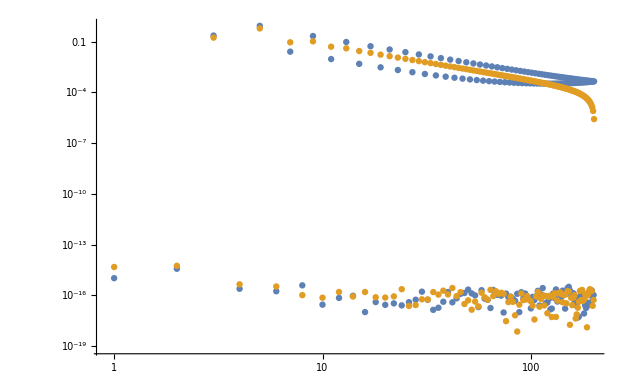

```mathematica
ListLogLogPlot[{Abs[dctStep], Abs[dctTanh]}, PlotRange->All]
```

```mathematica
(*Generate fourier tranform*)
```

```mathematica
f1[x_]:= Piecewise[{{Abs[Sin[2 π x/10]]-0.5, 0≤x≤10}},0]
f2[x_, scale_]:= Piecewise[{{scale(Sin[2 π x/6-0.5]), 0≤x≤10}},0]
```

```mathematica
fPlot[scale_]:=Plot[{f1[x], f2[x, scale]}, {x, -5 ,15}]
```

```mathematica
Manipulate[fPlot[k], {k, 0.3, 0.45}]
```

```mathematica
scalefactor = 0.2;
```

```mathematica
FT1[ω]=Simplify[FourierTransform[f1[x], x,ω ]Conjugate[FourierTransform[f1[x], x,ω ]]//ComplexExpand];
FT2[ω]=Simplify[FourierTransform[f2[x, scalefactor ], x,ω ]Conjugate[FourierTransform[f2[x, scalefactor ], x,ω ]]//ComplexExpand];
```

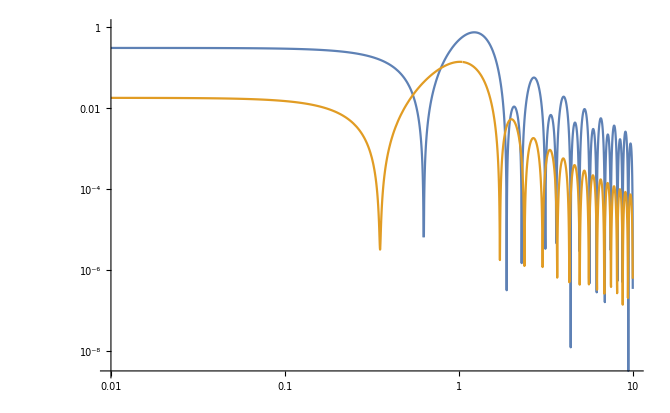

```mathematica
LogLogPlot[ {Abs[FT1[ω]], Abs[FT2[ω]]}, {ω, 0.01,10}]
```